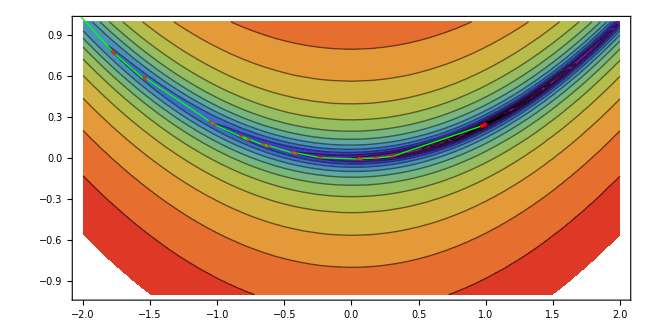

```mathematica
pts = {{-2.0000,1.5000},{-2.2206,1.2786},{-2.4297,1.4838},{-1.7789,0.7821},{-1.7653,0.7680},{-1.5432,0.5770},{-1.5394,0.5911},{-1.0509,0.2676},{-1.0176,0.2471},{-0.7694,0.1324},{-0.8200,0.1620},{-0.6201,0.0832},{-0.6539,0.1027},{-0.4103,0.0313},{-0.4365,0.0445},{-0.2353,0.0044},{0.0770,-0.0067},{0.0532,-0.0012},{0.1801,0.0011},{0.3064,0.0144},{0.9731,0.2377},{0.9735,0.2369},{0.9735,0.2369},{0.9955,0.2475},{0.9954,0.2477},{0.9954,0.2477}};
ContourPlot[(1-x)^2+100*(4y-x^2)^2,{x,-2,2},{y,-1,1},AspectRatio->{1}, Epilog->{Green,Line[pts],Opacity[0.5],PointSize[Medium],Red,Point[pts]},Contours->Table[2^i,{i,-20,20}],ColorFunction->(ColorData["Rainbow"][(Log[2,#]/12)]&),ColorFunctionScaling->False]
```